```mathematica
用动画模拟一个粒子的二维随机运动
```

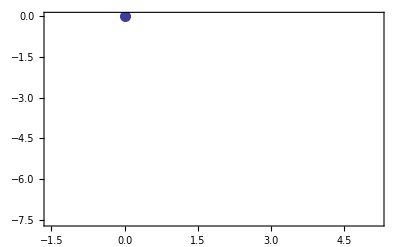

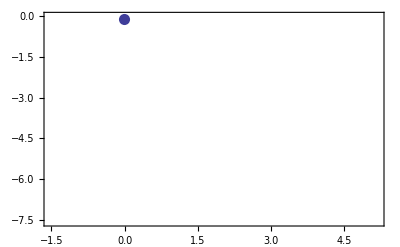

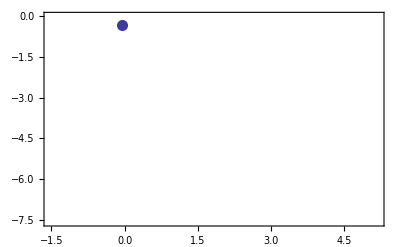

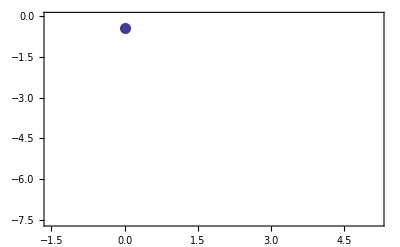

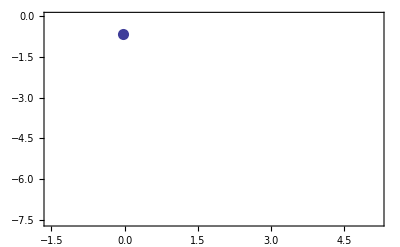

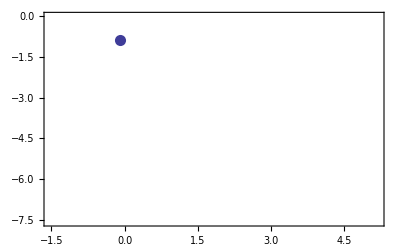

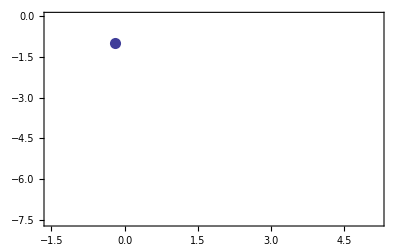

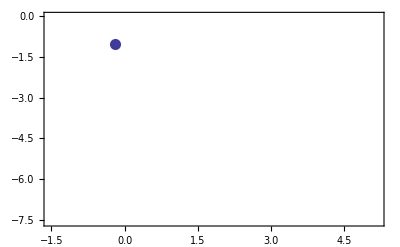

-Graphics-

-Graphics-

-Graphics-

«69 more identical outputs»

```mathematica
dis=NormalDistribution[0,1];
m=1000;δt=0.1;time=(m-1)*δt;α=0.5;
f1=Table[RandomReal[dis],{m}];
f2=Table[RandomReal[dis],{m}];
f1=Table[{δt*(i-1),f1[[i]]},{i,m}];
f2=Table[{δt*(i-1),f2[[i]]},{i,m}];
f1=Interpolation[f1];
f2=Interpolation[f2];
equs={x''[t]+α*x'[t]==f1[t],x[0]==0,
x'[0]==0,y''[t]+α*y'[t]==f2[t],y[0]==0,
y'[0]==0};
s=NDSolve[equs,{x,y},{t,0,time},MaxSteps->∞];
sample=200;  δt=time/(sample-1);
xsignal=Table[x[(i-1)*δt]/.s[[1]],{i,sample}];
x1=Min[xsignal];x2=Max[xsignal];
ysignal=Table[y[(i-1)*δt]/.s[[1]],{i,sample}];
y1=Min[ysignal];y2=Max[ysignal];
Do[
g=ListPlot[{{xsignal[[i]],ysignal[[i]]}},
PlotStyle->PointSize[0.02],
PlotRange->{{x1,x2},{y1,y2}},Axes->False,
Ticks->None,Frame->True];Print[g],
{i,sample}]
Clear[dis,m,δt,time,f1,f2,equs,s,x,y]
```

```mathematica
模拟多粒子的二维运动
```

```mathematica
dis=NormalDistribution[0,1];
n=20;m=1000;δt=0.1;time=(m-1)*δt;α=0.5;
f1=Table[RandomReal[dis] ,{i,n},{j,m}];
f1=Table[{δt*(i-1),f1[[j,i]]},{j,n},{i,m}];
f1=Table[Interpolation[f1[[i]]],{i,n}];
f2=Table[RandomReal[dis] ,{i,n},{j,m}];
f2=Table[{δt*(i-1),f2[[j,i]]},{j,n},{i,m}];
f2=Table[Interpolation[f2[[i]]],{i,n}];
equs=
Table[{x''[t]+α*x'[t]==f1[[i]][t],x[0]==0,
x'[0]==0,y''[t]+α*y'[t]==f2[[i]][t],
y[0]==0,y'[0]==0},{i,n}];
s=Table[NDSolve[equs[[i]],{x,y},{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];s=Partition[s,2];
sample=100;δt=time/(sample-1);
fig=total={};
Do[
section=
Table[{x[δt*(i-1)],y[δt*(i-1)]}/.s[[j]],
{j,n}];AppendTo[total,section],{i,sample}]
Do[
g=ListPlot[total[[i]],
PlotStyle->PointSize[0.02],Frame->True,
PlotRange->{{-15,15},{-15,15}},Axes->False];
AppendTo[fig,g];Print[g],
{i,sample}]
Export["e:/data/2d-Brown.gif",fig]
Clear[dis,time,equs,s,total,x,y,fig,g]
```

-Graphics-

-Graphics-

-Graphics-

«97 more identical outputs»

e:/data/2d-Brown.gif